## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"];
```

## Functions and PSF

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### FindParticles (updated to remove adjacentbordercounts)

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,7]&; 
t2=track2//Flatten//Partition[#,7]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
ol={t1⟦All,{2,1,3,4,5,6,7}⟧,t2⟦All,{2,1,3,4,5,6,7}⟧}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_optional]

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color,FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Probability",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### TXYDiffusionPlotter[txylsits,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p2,msds2},
msds=Table[{#⟦1⟧,((#⟦2⟧)^2+(#⟦3⟧)^2)}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt,1}];
p1=Table[Mean/@msds[[i]],{i,1,Length[msds],1}]//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&;
p2={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue),shapeN,size]

```mathematica
InteractionAnalyzer[ca_,column_,shapeN_,size_]:=Module[{goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
goodi=1+Position[Table[Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0]/(Length[ca⟦i⟧]-1),{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@bca⟦goodi,1;;maxt,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### MyMSDPlotter[myColorParameter_,color_]

```mathematica
MyMSDPlotter[myColorParameter_,color_]:=Module[{msds,p1,p2,poz},
mycol=If[color=="Red"||color=="Darker[Yellow,0.2]"||color=="Purple"||color=="White",13,If[color=="Green"||color=="Cyan",15,17]];
If[myColorParameter≠{},
msds=Table[poz=myColorParameter[[j,1;;All,mycol;;mycol+1]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[myColorParameter],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->ToExpression[color]]&;
{p2,p1}
]
]
```

### My3DImager[dir_, fileNameHead_, myt_, myx_, myy_, myc_, dimxy_, dz_, rangez_] dz in nanometers, assuming pixels are 130 nm

```mathematica
My3DImager[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&;
myGrid=Grid[{{myImg3D//Image3DProjection[#,"YZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageRotate[#,-π/2]&,myImg3D//Image3DProjection[#,"XY"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),1.3 (2 dimxy +1) }]&},{, myImg3D//Image3DProjection[#,"XZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageReflect[#,Left->Right]&}}]
]
```

```mathematica
My3DImagerRaw[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&
]
```

### Handchecking Functions

### Trim Corrector Interpolation

```mathematica
myTrimBGCorrecterAll[centrim_]:=Module[{testimg,myDot=-Graphics-,myDotImg,myDotImgD,myDotImgDXY,p1,f,mySubImg,myCorImg,CC,A,x0,y0},
testimg=centrim;
myDotImg=ImageMultiply[myDot,testimg];
myDotImgD=ImageData@myDotImg;
myDotImgDXY=Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myDotImgD,{2}],1]//DeleteCases[#,x_/;x[[3]]==0]&;
f=Interpolation[myDotImgDXY,InterpolationOrder->1];
mySubImg=Image[Table[f[x,y],{y,1,15,1},{x,1,15,1}]];
myCorImg=ImageSubtract[testimg,mySubImg];
{{{CC,A,x0,y0}}}=GetTrimPeakIntFixedSigmaAll[{myCorImg},1.5];
p1=ListPlot3D[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myCorImg//ImageData,{2}],1]];
{centrim,myCorImg,mySubImg,Show[Plot3D[CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),{x,1,15},{y,1,15},PlotRange->All,Mesh->True,MeshStyle->{{Red,Thick}},PlotStyle->{Opacity[0]}],p1],A}

]
```

```mathematica
myTrimBGCorrecter[centrim_]:=Module[{testimg,myDot=-Graphics-,myDotImg,myDotImgD,myDotImgDXY,p1,f,mySubImg,myCorImg,CC,A,x0,y0},
testimg=centrim;
myDotImg=ImageMultiply[myDot,testimg];
myDotImgD=ImageData@myDotImg;
myDotImgDXY=Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myDotImgD,{2}],1]//DeleteCases[#,x_/;x[[3]]==0]&;
f=Interpolation[myDotImgDXY,InterpolationOrder->1];
mySubImg=Image[Table[f[x,y],{y,1,15,1},{x,1,15,1}]];
myCorImg=ImageSubtract[testimg,mySubImg];
{{{CC,A,x0,y0}}}=GetTrimPeakIntFixedSigmaAll[{myCorImg},1.5];
p1=ListPlot3D[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myCorImg//ImageData,{2}],1]];
{A,myCorImg//ImageData//Flatten//Flatten//Total}

]
```

### Species Plot Function for FSXXLMS2 & SFXXLMS2

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

I want to make a function that can look in each channel and try to find a particle. After it does this I want it to do the donut to all channels (RGB). I want the output to be a list of Red Only, Yellow, White, and Purple spots. Within this list will be the RGB trims with the RGB donut intensity. Should have a list length of 3 and each one will be the how many spots there are.

```mathematica
imgmask=Table[1,{i,1,15,1},{j,1,15,1}]//Image;
```

```mathematica
SpeciesPlotData[mySpots_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.5,0.12,imgmask,{1,100}],x_/;6≤x[[1]]≤9.8];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,4},1.75,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.5];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤9.8&&6≤tempGPos[[1,2]]≤9.8,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.5&&6≤tempBPos[[1,2]]≤8.5,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntG,tempIntB}}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesPlotData[mySpots_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos,mytempIntR,bgtempIntR,tempIntR},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntR=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,1]];
bgtempIntR=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,1]];
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntR=mytempIntR/diskSize-bgtempIntR/ringSize;
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.5,0.12,imgmask,{1,100}],x_/;6≤x[[1]]≤9.8];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,12},1.75,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.5];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤9.8&&6≤tempGPos[[1,2]]≤9.8,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.5&&6≤tempBPos[[1,2]]≤8.5,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesPlotDataFN[mySpots_,mySpotFNs_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos,mytempIntR,bgtempIntR,tempIntR},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntR=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,1]];
bgtempIntR=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,1]];
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntR=mytempIntR/diskSize-bgtempIntR/ringSize;
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.5,0.12,imgmask,{1,100}],x_/;6≤x[[1]]≤9.8];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,12},1.75,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.5];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤9.8&&6≤tempGPos[[1,2]]≤9.8,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.5&&6≤tempBPos[[1,2]]≤8.5,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotFNs[[spot]]}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotFNs[[spot]]}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotFNs[[spot]]}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotFNs[[spot]]}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesPlotDataFN[HCRedTracks_,myImageInterval_,my488and561Interval_]:=Module[{mytempSpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,mytempInts,mytempCellFN,tempGPos,tempBPos,tempGSpot,tempBSpot},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
Table[mytempSpots=HCRedTracks[[cell,3,spot,2]];
mytempInts=HCRedTracks[[cell,3,spot,3]];
mytempCellFN=HCRedTracks[[cell,2]];
tempGPos=Cases[FindParticlesWeighted[(mytempSpots[[2]]//Mean)//ImageAdjust,{1,12},1.5,0.12,imgmask,{1,100}],x_/;6≤x[[1]]≤9.8];
tempBPos=Cases[FindParticlesWeighted[(mytempSpots[[3]]//Mean)//ImageAdjust,{1,12},1.75,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.5];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤9.8&&6≤tempGPos[[1,2]]≤9.8,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.5&&6≤tempBPos[[1,2]]≤8.5,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{cell,spot,mytempSpots,Range[2,Length@mytempSpots[[1]] myImageInterval,myImageInterval my488and561Interval],mytempInts,mytempCellFN}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{cell,spot,mytempSpots,Range[2,Length@mytempSpots[[1]] myImageInterval,myImageInterval my488and561Interval],mytempInts,mytempCellFN}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{cell,spot,mytempSpots,Range[2,Length@mytempSpots[[1]] myImageInterval,myImageInterval my488and561Interval],mytempInts,mytempCellFN}],
tempRedOnlyList=Append[tempRedOnlyList,{cell,spot,mytempSpots,Range[2,Length@mytempSpots[[1]] myImageInterval,myImageInterval my488and561Interval],mytempInts,mytempCellFN}]]]],{cell,1,Length@HCRedTracks,1},{spot, 1, Length@HCRedTracks[[cell,3]],1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesSFPlotData[mySpots_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.8,0.14,imgmask,{1,100}],x_/;6≤x[[1]]≤8.5];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,4},1,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.8];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤8.5&&6≤tempGPos[[1,2]]≤8.5,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.8&&6≤tempBPos[[1,2]]≤8.8,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntG,tempIntB}}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntG,tempIntB}}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesSFPlotData[mySpots_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos,mytempIntR,bgtempIntR,tempIntR},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntR=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,1]];
bgtempIntR=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,1]];
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntR=mytempIntR/diskSize-bgtempIntR/ringSize;
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.9,0.14,imgmask,{1,100}],x_/;6≤x[[1]]≤8.2];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,4},1,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.8];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤8.2&&6≤tempGPos[[1,2]]≤8.2,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.8&&6≤tempBPos[[1,2]]≤8.8,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB}}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
SpeciesSFPlotDataFN[mySpots_,mySpotsFN_]:=Module[{mytempSpots=mySpots,tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList,ringMask,diskMask,ringSize,diskSize,mytempIntB,bgtempIntB,mytempIntG,bgtempIntG,tempIntB,tempIntG,tempRSpot,tempGSpot,tempBSpot,tempGPos,tempBPos,mytempIntR,bgtempIntR,tempIntR},
tempRedOnlyList={};
tempYellowList={};
tempWhiteList={};
tempPurpleList={};
ringMask=Image[DiskMatrix[6,{15,15}]-DiskMatrix[3,{15,15}] ];
diskMask=Image[DiskMatrix[2,{15,15}] ];
ringSize=ringMask//ImageData//Total//Total;
diskSize=diskMask//ImageData//Total//Total;
Table[
mytempIntR=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,1]];
bgtempIntR=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,1]];
mytempIntB=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,3]];
bgtempIntB=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,3]];
mytempIntG=Total[Flatten[ImageData[ImageMultiply[diskMask,#]]]]&@mytempSpots[[spot,2]];
bgtempIntG=Total[Flatten[ImageData[ImageMultiply[ringMask,#]]]]&@mytempSpots[[spot,2]];
tempIntR=mytempIntR/diskSize-bgtempIntR/ringSize;
tempIntB=mytempIntB/diskSize-bgtempIntB/ringSize;
tempIntG=mytempIntG/diskSize-bgtempIntG/ringSize;
tempGPos=Cases[FindParticlesWeighted[mytempSpots[[spot,2]]//ImageAdjust,{1,12},1.9,0.14,imgmask,{1,100}],x_/;6≤x[[1]]≤8.2];
tempBPos=Cases[FindParticlesWeighted[mytempSpots[[spot,3]]//ImageAdjust,{1,4},1,0.13,imgmask,{1,100}],x_/;6≤x[[1]]≤8.8];
tempGSpot=If[Length@tempGPos≠0,If[6≤tempGPos[[1,1]]≤8.2&&6≤tempGPos[[1,2]]≤8.2,tempGPos,{}],{}];
tempBSpot=If[Length@tempBPos≠0,If[6≤tempBPos[[1,1]]≤8.8&&6≤tempBPos[[1,2]]≤8.8,tempBPos,{}],{}];
If[Length@tempGSpot>0&&Length@tempBSpot>0,tempWhiteList=Append[tempWhiteList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotsFN[[spot]]}],If[Length@tempGSpot>0&&Length@tempBSpot==0,tempYellowList=Append[tempYellowList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotsFN[[spot]]}],If[Length@tempGSpot==0&&Length@tempBSpot>0,tempPurpleList=Append[tempPurpleList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotsFN[[spot]]}],tempRedOnlyList=Append[tempRedOnlyList,{mytempSpots[[spot]],{tempIntR,tempIntG,tempIntB},mySpotsFN[[spot]]}]]]],{spot, 1, Length@mytempSpots,1}];
{tempRedOnlyList,tempYellowList,tempWhiteList,tempPurpleList}]
```

```mathematica
FilterGlobules[myBlueSpots_]:=Module[{tempGoodList,tempCrapList,mytempSpots=myBlueSpots},
tempGoodList={};
tempCrapList={};
Table[
If[Length@(FindParticlesWeighted[mytempSpots[[spot,1,3]]//ImageAdjust,{1,12},1.3,0.083,imgmask,{1,32}])==0,tempCrapList=Append[tempCrapList,{mytempSpots[[spot]]}],tempGoodList=Append[tempGoodList,{mytempSpots[[spot]]}]]
,{spot,1,Length@mytempSpots,1}];
{tempGoodList,tempCrapList}]
```

### ErrorBar

```mathematica
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
```

### Get Trim Peak Intensity without Fixing the Sigma

```mathematica
GetTrimPeakIntSigmaIntergrate[myMeanTrim_]:=Module[{myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
{A √(2 π) a/.myTrimtempGauss[[fit]]["BestFitParameters"]},{fit,1,Length@myTrimtempPos,1}]]
```

### Get Trim Peak Intensity with Fixed Sigma

```mathematica
GetTrimPeakIntFixedSigma[myMeanTrim_,sigma_]:=Module[{x0,y0,CC,A,myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0},{A,0},{x0,8},{y0,8}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
{A /.myTrimtempGauss[[fit]]["BestFitParameters"]},{fit,1,Length@myTrimtempPos,1}]]
```

```mathematica
GetTrimPeakIntFixedSigmaAll[myMeanTrim_,sigma_]:=Module[{x0,y0,CC,A,myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0},{A,0},{x0,8},{y0,8}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
{{CC,A,x0,y0} /.myTrimtempGauss[[fit]]["BestFitParameters"]},{fit,1,Length@myTrimtempPos,1}]]
```

```mathematica
GetTrimPeakIntFixedSigma95Conf[myMeanTrim_,sigma_]:=Module[{x0,y0,CC,A,myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0},{A,0},{x0,8},{y0,8}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
Flatten@{A √(2 π) sigma/.myTrimtempGauss[[fit]]["BestFitParameters"],MyErrorPropagator[x y,A/.myTrimtempGauss[[fit]]["BestFitParameters"],sigma/.myTrimtempGauss[[fit]]["BestFitParameters"],1,Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals",ConfidenceLevel-> .95][[2]],Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals",ConfidenceLevel-> .95][[4]],1]},{fit,1,Length@myTrimtempPos,1}]]
```

### Get Integrated Trim Peak Intensity and Sigma and Peak Intensity 95% Confidence Interval Error Propagated

```mathematica
GetTrimPeakIntSigmaIntergrate95Conf[myMeanTrim_]:=Module[{myTrim=myMeanTrim,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrim[[spot]]],{spot,1,Length@myTrim,1}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
Table[myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
Flatten@{A √(2 π) a/.myTrimtempGauss[[fit]]["BestFitParameters"],MyErrorPropagator[x y,A/.myTrimtempGauss[[fit]]["BestFitParameters"],a/.myTrimtempGauss[[fit]]["BestFitParameters"],1,Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals",ConfidenceLevel-> .95][[2]],Differences@myTrimtempGauss[[fit]]["ParameterConfidenceIntervals",ConfidenceLevel-> .95][[4]],1]},{fit,1,Length@myTrimtempPos,1}]]
```

### Remove Trims which spots are large than 2 sigma for x position

```mathematica
GetGoodTrims[myTrims_]:=Module[{myTrimAllSpotsF=myTrims,myTrimtempData,myTrimtempPos,myTrimtempGauss},
myTrimtempData=Table[ImageData[myTrimAllSpotsF[[spot]]],{spot,1,Length@myTrimAllSpotsF}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
Part[myTrimAllSpotsF,Flatten@Position[Table[myTrimtempGauss⟦i⟧["ParameterConfidenceIntervals"],{i,1,Length@myTrimtempGauss,1}][[All,4,2]],x_/;x<2]]]
```

### Remove Trims which spots are larger than 2 sigma for x position and also taking the corresponding Blue Trim (For when there is no existing blue spot)

```mathematica
GetGood0TrimsAndFSTrims[my0Trims_,myFSTrims_]:=Module[{myTrimAllSpotsF=my0Trims,myTrimtempData,myTrimtempPos,myTrimtempGauss,myTrimFSAllSpotsF=myFSTrims},
myTrimtempData=Table[ImageData[myTrimAllSpotsF[[spot]]],{spot,1,Length@myTrimAllSpotsF}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
{Part[myTrimAllSpotsF,Flatten@Position[Table[myTrimtempGauss⟦i⟧["ParameterConfidenceIntervals"],{i,1,Length@myTrimtempGauss,1}][[All,4,2]],x_/;x<2]],Part[myTrimFSAllSpotsF,Flatten@Position[Table[myTrimtempGauss⟦i⟧["ParameterConfidenceIntervals"],{i,1,Length@myTrimtempGauss,1}][[All,4,2]],x_/;x<2]]}]
```

### FilterFitOutlier

```mathematica
(*(* This function removes outliers based on intensity, 90% confidence interval of xy positions and the size of sigma; Tatsuya's Recipe for best Gaussian Data: maxDxy_ = 5 and maxSig_= 20*)
FilterFitOutlier[mySpotsFit_,maxDxy_,maxSig_]:=Module[{idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
idxInt=Position[mySpotsFit⟦All,All,4,2,1⟧,x_/;x<0||x>2];
idxX90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,1⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxY90Conf=Position[(Differences/@#&/@mySpotsFit⟦All,All,5,1,2⟧)⟦All,All,1⟧,x_/;x>maxDxy];
idxSigX=Position[mySpotsFit⟦All,All,4,3,1⟧,x_/;Abs@x>maxSig];
idxSigY=Position[mySpotsFit⟦All,All,4,3,2⟧,x_/;Abs@x>maxSig];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[mySpotsFit,idxOutliers]
]*)
```

### ErrorPropagator

```mathematica
MyErrorPropagator[f_,xmean_,ymean_,zmean_,σx_,σy_,σz_]:=Evaluate[((D[f,x]^2 σx^2+D[f,y]^2 σy^2+D[f,z]^2 σz^2)^(1/2))]/.{x-> xmean,y-> ymean,z-> zmean}
```

### Fitting Trims and Filtering Out Bad Spots, also using the 0 frame to take the -1 frame trims too, Usually use maxDxy of 5 and maxSig of 20!

```mathematica
FilterTrimFitOutlier0andFS[my0Trims_,myFSTrims_,maxDxy_,maxSig_]:=Module[{myTrimAllSpotsF=my0Trims,myTrimFSAllSpotsF=myFSTrims,myTrimtempData,myTrimtempPos,myTrimtempGauss,idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
myTrimtempData=Table[ImageData[myTrimAllSpotsF[[spot]]],{spot,1,Length@myTrimAllSpotsF}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
idxInt=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[2,1]],{i,1,Length@myTrimtempGauss,1}],x_/;x<0||x>2];
idxX90Conf=Position[Flatten[Table[Differences@#&@myTrimtempGauss[[i]]["ParameterConfidenceIntervals"][[3]],{i,1,Length@myTrimtempGauss,1}]],x_/;x>5];
idxY90Conf=Position[Flatten[Table[Differences@#&@myTrimtempGauss[[i]]["ParameterConfidenceIntervals"][[5]],{i,1,Length@myTrimtempGauss,1}]],x_/;x>5];
idxSigX=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[4,1]],{i,1,Length@myTrimtempGauss,1}],x_/;Abs@x>20];
idxSigY=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[6,1]],{i,1,Length@myTrimtempGauss,1}],x_/;Abs@x>20];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
{Delete[myTrimAllSpotsF,idxOutliers],Delete[myTrimFSAllSpotsF,idxOutliers]}
]
```

```mathematica
FilterTrimFitOutlier[my0Trims_,maxDxy_,maxSig_]:=Module[{myTrimAllSpotsF=my0Trims,myTrimtempData,myTrimtempPos,myTrimtempGauss,idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY,idxOutliers},
myTrimtempData=Table[ImageData[myTrimAllSpotsF[[spot]]],{spot,1,Length@myTrimAllSpotsF}];
myTrimtempPos=Table[Flatten[MapIndexed[{#2[[2]]1,#2[[1]]1,#1}&,myTrimtempData[[i]],{2}],1],{i,1,Length@myTrimtempData}];
myTrimtempGauss=Quiet[Table[NonlinearModelFit[myTrimtempPos[[i]],CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,0},{x0,8},{a,1},{y0,8},{b,1}},{x,y}],{i,1,Length@myTrimtempPos,1}]];
idxInt=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[2,1]],{i,1,Length@myTrimtempGauss,1}],x_/;x<0||x>2];
idxX90Conf=Position[Flatten[Table[Differences@#&@myTrimtempGauss[[i]]["ParameterConfidenceIntervals"][[3]],{i,1,Length@myTrimtempGauss,1}]],x_/;x>5];
idxY90Conf=Position[Flatten[Table[Differences@#&@myTrimtempGauss[[i]]["ParameterConfidenceIntervals"][[5]],{i,1,Length@myTrimtempGauss,1}]],x_/;x>5];
idxSigX=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[4,1]],{i,1,Length@myTrimtempGauss,1}],x_/;Abs@x>20];
idxSigY=Position[Table[myTrimtempGauss[[i]]["ParameterTableEntries"][[6,1]],{i,1,Length@myTrimtempGauss,1}],x_/;Abs@x>20];
idxOutliers=Union[idxInt,idxX90Conf,idxY90Conf,idxSigX,idxSigY];
Delete[myTrimAllSpotsF,idxOutliers]]
```

### TrimsForSpeciesPlot[outputDirectory, Color, goodspotlist]

```mathematica
TrimsForSpeciesPlot[outDir_,myColor_,goodspotlist_]:=Module[{upto,myIs,temp,outName},
Table[
upto=StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max;
myIs=GetTrimPeakIntFixedSigma[goodspotlist[[spot,3]],1.5]//Flatten;
temp=<<(StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"_sorted"]//Max]<>"_FixedSigma"<>myColor<>"ColorParameters.dat")⟦goodspotlist[[spot,2]]⟧;
outName=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotNumberRGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_Xred_"<>ToString[temp[[1,13]]]<>"_Yred_"<>ToString[temp[[1,14]]]<>"_FixedSigma1p5Ired_"<>ToString[myIs[[1]]]<>"_FixedSigma1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";
Export[outDir<>"\\"<>outName,ColorCombine[goodspotlist[[spot,3]],"RGB"]],{spot,1,Length@goodspotlist,1}]
]
```

```mathematica
TrimsForSpeciesPlot[myColor_,goodspotlist_]:=Module[{upto,myIs,temp,aF,outName,outDir},
Table[
aF="\\\?\\"<>StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max]<>"\\";
upto=StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max;
myIs=GetTrimPeakIntFixedSigma[goodspotlist[[spot,3]],1.5]//Flatten;
temp=<<(StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"_sorted"]//Max]<>"_FixedSigma"<>myColor<>"ColorParameters.dat")⟦goodspotlist[[spot,2]]⟧;
outName=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotN"<>ToString[spot]<>"RGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_XR_"<>ToString[temp[[1,13]]]<>"_YR_"<>ToString[temp[[1,14]]]<>"_FixSig1p5IR_"<>ToString[myIs[[1]]]<>"_FixSig1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";
outDir=StringTake[goodspotlist[[1,1]],StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max];
Export[aF<>outName,ColorCombine[goodspotlist[[spot,3]],"RGB"]],{spot,1,Length@goodspotlist,1}]
]
```

```mathematica
TrimsForSpeciesPlot[myColor_,goodspotlist_]:=Module[{upto,myIs,temp,aF,outName,outDir},
Table[
aF="\\\?\\"<>StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max]<>"\\";
upto=StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max;
myIs=GetTrimPeakIntFixedSigma[goodspotlist[[spot,3]],1.5]//Flatten;
temp=<<(StringTake[goodspotlist[[spot,1]],(StringPosition[goodspotlist[[spot,1]],"my"<>myColor]//Min)-2]<>"_FixedSigma"<>myColor<>"ColorParameters.dat")⟦goodspotlist[[spot,2]]⟧;
outName=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotN"<>ToString[spot]<>"RGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_XR_"<>ToString[temp[[1,13]]]<>"_YR_"<>ToString[temp[[1,14]]]<>"_FixSig1p5IR_"<>ToString[myIs[[1]]]<>"_FixSig1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";
outDir=StringTake[goodspotlist[[1,1]],StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max];
Export[aF<>outName,ColorCombine[goodspotlist[[spot,3]],"RGB"]],{spot,1,Length@goodspotlist,1}]
]
```

```mathematica
TrimsForSpeciesPlot[outDir_,myColor_,goodspotlist_]:=Module[{upto,myIs,temp,outName},
Table[
upto=StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max;
myIs=GetTrimPeakIntFixedSigma[goodspotlist[[spot,3]],1.5]//Flatten;
temp=<<(StringTake[goodspotlist[[spot,1]],(StringPosition[goodspotlist[[spot,1]],"my"<>myColor]//Min)-2]<>"_FixedSigma"<>myColor<>"AllParameters.m")⟦goodspotlist[[spot,2]]⟧;
outName=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotN"<>ToString[spot]<>"RGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_XR_"<>ToString[temp[[1,13]]]<>"_YR_"<>ToString[temp[[1,14]]]<>"_FixSig1p5IR_"<>ToString[myIs[[1]]]<>"_FixSig1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";
Export[outDir<>"\\"<>outName,ColorCombine[goodspotlist[[spot,3]],"RGB"]],{spot,1,Length@goodspotlist,1}]
]
```

```mathematica
(*goodspotlist=goodredonlyspotlist;*)
```

```mathematica
(*spot=180;*)
```

```mathematica
(*aF="\\\?\\"<>StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max]<>"\\";
upto=StringPosition[goodspotlist[[spot,1]],"Analysis"]//Max;
myIs=GetTrimPeakIntFixedSigma[goodspotlist[[spot,3]],1.5]//Flatten;*)
```

```mathematica
(*aF*)
```

```mathematica
(*myColor="RedOnly";*)
```

```mathematica
(*temp=<<(StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"_sorted"]//Max]<>"_FixedSigma"<>myColor<>"ColorParameters.dat")⟦goodspotlist[[spot,2]]⟧;
outName1=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotN"<>ToString[spot]<>"RGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_XR_"<>ToString[temp[[1,13]]]<>"_YR_"<>ToString[temp[[1,14]]]<>"_FixSig1p5IR_"<>ToString[myIs[[1]]]<>"_FixSig1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";*)
```

```mathematica
(*outName1*)
```

```mathematica
(*StringPosition[goodspotlist[[spot,1]],"_sorted"]//Max*)
```

```mathematica
(*StringTake[goodspotlist[[spot,1]],StringPosition[goodspotlist[[spot,1]],"_sorted"]//Max]*)
```

```mathematica
(*goodspotlist[[spot,1]]*)
```

```mathematica
(*(StringPosition[goodspotlist[[spot,1]],"my"<>myColor]//Min)-2*)
```

```mathematica
(*temp=<<(StringTake[goodspotlist[[spot,1]],(StringPosition[goodspotlist[[spot,1]],"my"<>myColor]//Min)-2]<>"_FixedSigma"<>myColor<>"ColorParameters.dat")⟦goodspotlist[[spot,2]]⟧;
outName=StringDrop[StringTake[goodspotlist[[spot,1]],{upto+2,StringLength[goodspotlist[[spot,1]]]}],-2]<>"SpotN"<>ToString[spot]<>"RGB_"<>ToString[temp[[1,1]]]<>"_"<>ToString[temp[[1,2]]]<>"_"<>ToString[temp[[1,3]]]<>"_FrameN_"<>ToString[temp[[1,4]]]<>"to"<>ToString[temp[[5,4]]]<>"_XR_"<>ToString[temp[[1,13]]]<>"_YR_"<>ToString[temp[[1,14]]]<>"_FixSig1p5IR_"<>ToString[myIs[[1]]]<>"_FixSig1p5Igreen_"<>ToString[myIs[[2]]]<>"_FixedSigma1p5Iblue_"<>ToString[myIs[[3]]]<>".tif";*)
```

```mathematica
(*outName*)
```

```mathematica
(*outName==outName1*)
```

## Analysis

### Reading in Maximum Projection Tif Images

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

This will partition a three color movie, if the movie is not three colors then an error will occur

```mathematica
mymovie=If[StringTake[FileBaseName[mymovie],4]=="AVG_",StringReplace[mymovie,"AVG_"->""],mymovie];
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

This is making an average image of the movie to help make a mask

```mathematica
If[FileExistsQ[analysisFolder<>"_avg.tif"]==True,
avgImg=Import[analysisFolder<>"_avg.tif"];,
avgImg=Mean/@myColMovie;
Export[(analysisFolder<>"_avg.tif"),avgImg]];
```

### Make Masks of Cytoplasm and Nucleus

Choose a nice threshold first such that you can make out the shape of the cell

```mathematica
Manipulate[avgImg⟦2⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,0.2,0.001}]
```

Run this next line to see your selected average image with the desired threshold. Click on the image and select the mask tool to create and copy the mask image below into the “mymask”

```mathematica
ImageAdjust[avgImg⟦2⟧,{0,0,1},thtemp]
```

-Graphics-

This will export out the mask image to the analysis folder

```mathematica
mymask=-Graphics-;
Export[analysisFolder<>"_mask.tif",mymask];
```

### Creating Transformation Function (need to only run this once per imaging day to get a transformation function for that imaging day)

```mathematica
dirBeads=DirectoryName[mymovie]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

20 red particles and 19 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

General::munfl: (1.75426×10^-307)/109.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0013736^109.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.06029×10^-307)/109.5 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.107421,TransformationFunction[(1.00192 | -0.00474023 | 2.93625
0.00317464 | 1.00359 | -1.52968
1.01473×10^-6 | 6.17355×10^-8 | 1.)],Distance Before Correction | Distance After Correction
1.56028 | 0.15183
1.36684 | 0.124857
1.63938 | 0.020619
0.967872 | 0.0388495
1.35921 | 0.134548
1.42057 | 0.130699
1.01275 | 0.178449
1.41729 | 0.255172
1.82806 | 0.0858955
1.67689 | 0.0542119
1.80461 | 0.172144
2.41014 | 0.0343045
2.14091 | 0.213774
2.26445 | 0.0896564
2.95558 | 0.0135786
2.78519 | 0.0843578
3.21532 | 0.10184
3.1102 | 0.12743
3.13285 | 0.0287852}

```mathematica
Export[DirectoryName[mymovie]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

### Running z-average (use this if you want to make a running average of the movie; I usually do not do a rolling average so I leave the avgFrameN = 1)

```mathematica
avgFrameN=1;
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,1,Length[myColMovieRunAv],1},{frame,1,myMaxN,1},{threshold,0,0.2,0.001}];
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

7 red particles and 7 green particles were found.

### Reading in Parameters (only if parameters exist)

```mathematica
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
redRunAvp=<<(analysisFolder<>"_redspots.dat");
```

Syntax::sntue: Unexpected end of file (probably unfinished expression)  (line 43001 of "C:\Users\TSlab\Dropbox\Work Folder\Postdoc\Munsky Lab\_mirroredFiXiE\20190909_u2os_multiplex\smFLAG-KDM5B\Analysis\MAX_Cell01_redspots.dat").

```mathematica
myredtracks=<<(analysisFolder<>"_redtracks.dat");
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

$Aborted

```mathematica
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
mymask=<<(analysisFolder<>"_mymask.dat");
```

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
myCytImg=myCytMask;
```

```mathematica
myNucImg=myNucMask;
```

### Find Red Particles from Running z - averaged Movie (Red laser)

```mathematica
(* redRunAvp is list of {{x1,y1},{x2,y2}....{xn,yn}} in each frame *)
```

Adjust threshold to see spots nicely

```mathematica
Manipulate[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thred={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦1⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,0.4,0.001}]
```

Choose a threshold setting to where you can see nice well defined spots that match the left image

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦1, 1⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,mymask],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦1, frame⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦1,frame⟧// ImageAdjust[#, {0, 0, 1}, thred]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],mymask],"Count",lo<#<hi&]},ImageSize->500],
Button["Choose parameters and CLICK",{mymaxred=max,bandpassred={lowpass,hipass},thred2=threshold,dotsizered={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,10,1},{{lo,5},0,20,1},{{hi,100},50,200,1}]
```

```mathematica
redRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],{i,1,myMaxN,1}];
StringForm["   `` red particles were found.",redRunAvp//Flatten[#,1]&//Length]
```

66417 red particles were found.

```mathematica
redComponentMask=Table[ImageTransformation[FindParticlesWeightedMask[myColMovieRunAv⟦1,i⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,mymask,dotsizered],myTfFuncInv,DataRange->Full],{i,1,myMaxN,1}];
```

This will show you the red spots that are being found in each frame (this has not linked them up yet)

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",redRunAvp>>analysisFolder<>"_redspots.dat";Export[analysisFolder<>"_redComponentMask.tif",redComponentMask];],
{frame,1,myMaxN,1}]
```

Just a plot to visualize the number of spots per frame

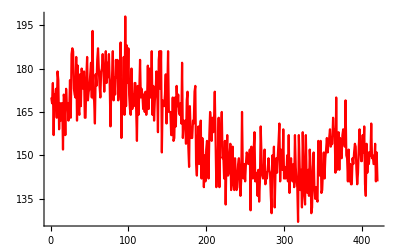

```mathematica
rSpotNPlot=Length/@redRunAvp//ListLinePlot[#,PlotStyle->Red]&
```

### Linking red tracks

This will link the tracks; set the pixel jump size that you will allow to link red spots; you can get more artifactual linked tracks if the maxJumpDistRed is higher than 5; having it too low will cause you to have partial/fragmented tracks

```mathematica
maxJumpDistRed=5;
my488and561Interval=2;
```

```mathematica
myredtracks=LinkTracks2[redRunAvp,maxJumpDistRed];
StringForm["`` red tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",myredtracks//Length,maxJumpDistRed,(Length/@myredtracks)//Mean//N]
```

4661 red tracks were found by allowing 5 pixel jump, and the average length of the tracks is 7.71573

```mathematica
myredtracks>>analysisFolder<>"_redtracks.dat";
```

This will filter out shorter tracks, I find that anything >40 helps to ensure you are tracking real RNA and not spot noise

```mathematica
shortestTrackRed=41;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
```

90 red tracks are longer than 41, and the average length of the long tracks is 67.9111

```mathematica
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

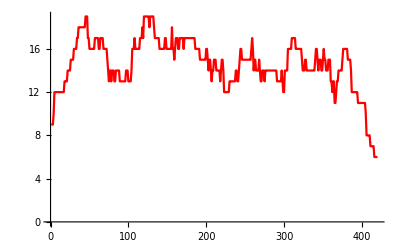

```mathematica
rSpotNPlot=Length/@mylongredtracksf//ListLinePlot[#,PlotStyle->Red]&
```

### Check all tracks (and double-check transformation function)

```mathematica
mylongredtracksColReg=mylongredtracks;
mylongredtracksColReg⟦All,All,2,2;;⟧=myTfFunc/@mylongredtracksColReg⟦All,All,2,2;;⟧;
Clear[mylongredtracksColRegf]
mylongredtracksColRegf=mylongredtracksColReg⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

### Linking red, blue, and green tracks

```mathematica
tracksr=Map[Append[#,{1,0,0}]&,mylongredtracksColReg,{2}];
tracksr⟦All,All,1⟧=Range@Length@tracksr;
```

## Fitting Red Tracks with Gaussian and Making Parameter File

#### Setting Parameters

```mathematica
pad=5;
myTrimSize=2*pad+1;
```

#### Fitting red tracks with Gaussian

This is doing an intial guassian fit of the red spots and their positions; I use this information for the positions of the spots below

```mathematica
{myRedAllParameters,myRedPos,myRedData}=ParticleFittingFixedSigma[myColMovie,1,tracksr,pad,myTrimSize,1.5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
{myRedAllParameters,myRedPos,myRedData}>>analysisFolder<>"_redfits.dat";
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

```mathematica
myRedAllParametersColReg=myRedAllParameters;
(*myRedAllParametersColReg⟦All,3;;4⟧=myTfFunc/@myRedAllParameters⟦All,3;;4⟧;*)
```

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
myRedAllParametersColRegLabeled=Insert[myRedAllParametersColReg,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaRedAllParameters.xls",myRedAllParametersColRegLabeled];
myRedAllParametersColReg>>(analysisFolder<>"_FixedSigmaRedAllParameters.m");
```

## Making RGB Trims from Red Tracks

This reads in the movie again if you need to; if it is already defined from running the code above then you do not need to run this

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

This will read in the movie and partition it as it does above; doesn’t need to be done if you have already defined it from above

```mathematica
mymovie=If[StringTake[FileBaseName[mymovie],4]=="AVG_",StringReplace[mymovie,"AVG_"->""],mymovie];
```

```mathematica
myColMovie=Import[mymovie]//Partition[#,3]&//Transpose;
If[DirectoryQ@(DirectoryName[mymovie]<>"Analysis\\")==False,CreateDirectory@(DirectoryName[mymovie]<>"Analysis\\")];
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
```

### Reading in all saved parameters

Reading in parameters from the above cell

```mathematica
analysisFolder=DirectoryName[mymovie]<>"Analysis\\"<>StringDrop[StringDelete[mymovie,DirectoryName[mymovie]],-4];
If[FileExistsQ[StringReplace[mymovie,"MAX"->"AVG_MAX"]]==True,
avgImg=Import[StringReplace[mymovie,"MAX"->"AVG_MAX"]];,
avgImg=Mean/@myColMovie;];
myavgImg=StringReplace[mymovie,"MAX"->"AVG_MAX"];
```

```mathematica
mymask=Import[analysisFolder<>"_mymask.dat"];
myavgImg=StringReplace[mymovie,"MAX"->"AVG_MAX"];
avgFrameN=IntegerPart[avgFrameN];
myTfFunc=Import[DirectoryName[mymovie]<>"TransformationFunction.m"];
myTfFuncRev=InverseFunction@myTfFunc;
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
myRedAllParametersColReg=myRedAllParameters;
myRedAllParametersColReg⟦All,3;;4⟧=Table[myRedAllParameters⟦i,3;;4⟧,{i,1,Length[myRedAllParameters],1}];
myRedParameterColRegSplit=myRedAllParametersColReg//SplitBy[#,First]&;
```

```mathematica
avgImg=Mean/@myColMovie;
avgColImg=ColorCombine[ImageAdjust/@{avgImg⟦1⟧,avgImg⟦2⟧,ConstantImage[0,ImageDimensions@avgImg⟦1⟧]}];
myRedParameterSplit=myRedAllParameters//SplitBy[#,First]&;(*Grouping tracks together from Parameter list*)
RedCentroid=Thread[{Range[Length[myRedParameterSplit]],Table[myRedParameterSplit⟦i,All,3;;4⟧//Mean,{i,1,Length[myRedParameterSplit],1}]}]; (*Taking the mean position of each grouped tracks*)
posRedLongTracks=Graphics[{Red,Circle[#,7]&/@(RedCentroid⟦All,2⟧),Table[Inset[RedCentroid⟦i,1⟧,RedCentroid⟦i,2⟧],{i,1,Length[RedCentroid],1}]}]; (*Making dumb little circles around the average position of each tracks*)
(*Manipulate[Show[myColMovieRunAv⟦1,start-1+frame⟧//ImageAdjust[#,{0,0,1},thred]&,posRedLongTracks],{frame,start,end,1}]*)
```

### Making Red Track Trims with either Blue and Green aligned to center of pad

```mathematica
myRedParameterSplitColReg=myRedAllParametersColReg//SplitBy[#,First]&;
myRedParameterSplitColReg>>analysisFolder<>"_myRedParameterSplitColReg.m"
```

```mathematica
pad2=7;
ClearAll[myRedParameterSplitColReg,TrimRed,TrimGreen,TrimBlue,Trim3Colors]
myRedParameterSplitColReg=myRedAllParametersColReg//SplitBy[#,First]&;
{TrimRed,TrimGreen,TrimBlue,Trim3Colors}=Table[Table[
tempTime=myRedParameterSplit⟦myi,i,2⟧;
tempCenter=Ceiling[(myRedParameterSplit⟦myi,i,3;;4⟧)];
tempCenterColReg=Ceiling[myTfFunc@myRedParameterSplitColReg⟦myi,i,3;;4⟧];
{tempRed,tempGreen,tempBlue}={
ImageTrim[myColMovie⟦1,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageTrim[myColMovie⟦2,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad2,tempCenterColReg+pad2-0.1}],
ImageTrim[myColMovie⟦3,tempTime+Ceiling[avgFrameN/2]-1⟧,{tempCenterColReg-pad2,tempCenterColReg+pad2-0.1}]};
{tempRed,tempGreen,tempBlue,ColorCombine[{ImageAdjust@tempRed,ImageAdjust@tempGreen,ImageAdjust@tempBlue}]},
{i,1,Length[myRedParameterSplit⟦myi⟧],1}]//Transpose,{myi,1,1Length[myRedParameterSplit],1}]//Transpose;
```

```mathematica
Thread[{TrimRed,TrimGreen,TrimBlue}]>>analysisFolder<>"_myRedTrackRGBTrims.m";
```

### Hand Checking all red tracks

Define all the myDirectories below here, only put the directories that have the same construct and the same imaging conditions that you want to handcheck below. Always change the my

```mathematica
myDirectories={("P:\\20190920_u2os_multiplex\\smFLAG-KDM5B-GBInterval_2\\Analysis"<>"\\")}; (*Input all analysis folder pathways here that already have the RedTrackRGBTrims from above and that are the same construct and same imaging intervals, make sure to add a \\ after the Analysis folder when inputting new folders*)
```

Showing the number of myRedTrackRGBTrims (cells) you have in this directory

```mathematica
Flatten@Table[FileNames[myDirectories[[directory]]<>"*_myRedTrackRGBTrims.m"],{directory,1,Length@myDirectories,1}]
```

{P:\20190920_u2os_multiplex\smFLAG-KDM5B-GBInterval_2\Analysis\MAX_Cell01_myRedTrackRGBTrims.m,P:\20190920_u2os_multiplex\smFLAG-KDM5B-GBInterval_2\Analysis\MAX_Cell02_myRedTrackRGBTrims.m}

Getting the file names of each cell in the directory and then uploading the RedRGBParameters made above

```mathematica
myRedRGBTrimsAllCellsFNs=Flatten@Table[FileNames[myDirectories[[directory]]<>"*_myRedTrackRGBTrims.m"],{directory,1,Length@myDirectories,1}];
myRedRGBParameterAllCellsFNs=Table[StringTake[myRedRGBTrimsAllCellsFNs[[cell]],(StringPosition[myRedRGBTrimsAllCellsFNs[[cell]],"my"]//Min)-2]<>"_myRedParameterSplitColReg.m",{cell,1,Length@myRedRGBTrimsAllCellsFNs,1}];
myRedParameterSplitColReg=Get[#]&/@myRedRGBParameterAllCellsFNs;
```

Counting the number of myRedParametersSplitColReg files, should be the same number as there are cells

```mathematica
Length@myRedParameterSplitColReg
```

2

Looking at the length of each track, each number is the length of the track for each spot (should all be over >40 in length)

```mathematica
Length/@myRedParameterSplitColReg[[1]]
```

{239,62,126,47,99,61,73,47,108,85,68,45,50,46,49,48,46,46,88,42,44,76,89,43,42,54,86,60,70,166,54,118,42,94,56,68,44,136,71,132,66,51,50,43,42,52,56,53,50,46,218,57,53,59,72,44,48,45,91,57,101,51,42,65,84,133,56,43,89,84,92,55,53,64,60,43,50,55,81,46,41,56,65,48,43,54,43,51,46,45}

Reading in the trims made above from each cell in this directory

```mathematica
myRedTrackRGBTrimsAllCells=Get[#]&/@myRedRGBTrimsAllCellsFNs;
```

```mathematica
Length/@myRedTrackRGBTrimsAllCells[[1,All,1]](*Is in the same order as up top need to make these both compatiable with reading in multiple directories!*)
```

{239,62,66,47,99,43,40,47,49,85,45,46,43,53,53,49,90,65,43,42,59,67,54,86,41,68,73,58,42,166,127,43,118,57,68,49,44,155,66,54,51,51,50,50,57,56,46,40,176,58,53,59,41,53,48,45,91,57,101,92,42,73,61,59,69,43,56,49,45,78,49,57,40,48,47,58,56,44,41}

Counting the number of myRedTrackRGBTrimsAllCells files, should be the same number as there are cells

```mathematica
Length@myRedTrackRGBTrimsAllCells
```

2

```mathematica
(*my488and561Interval=2;*)
(*myRedTrackRGBGaussIntAllCells=Table[
If[cell>2,my488and561Interval=3,my488and561Interval=2];GetTrimPeakIntFixedSigma95Conf[#,1.5]&/@myRedTrackRGBTrimsAllCells[[cell,spot,All,1;;All;;my488and561Interval]],{cell,1,Length@myRedTrackRGBTrimsAllCells,1},{spot,1,Length@myRedTrackRGBTrimsAllCells[[cell]],1}];*) (*Can use this if I have some cells with different 488 and 561 intervals*)
```

```mathematica
myRedRGBGaussIntAllCellsFNs=Table[StringTake[myRedRGBTrimsAllCellsFNs[[cell]],(StringPosition[myRedRGBTrimsAllCellsFNs[[cell]],"my"]//Min)-2]<>"_myRedTrackRGBGaussIntAllCells.m",{cell,1,Length@myRedRGBTrimsAllCellsFNs,1}];
```

Fitting the gaussian intensity of only frames that all fluorescences were being imaged; make sure to put the correct imaging interval below!   (should not have to run this again and can just skip down to the uploading if you have already done this step!)

```mathematica
my488and561Interval=2;
myRedTrackRGBGaussIntAllCells=Table[GetTrimPeakIntFixedSigma95Conf[#,1.5]&/@myRedTrackRGBTrimsAllCells[[cell,spot,All,1;;All;;my488and561Interval]],{cell,1,Length@myRedTrackRGBTrimsAllCells,1},{spot,1,Length@myRedTrackRGBTrimsAllCells[[cell]],1}];
```

Making file names for the gaussian fit information

Exporting the gaussian fit information because it takes a little while to run (should not have to run this again and can just skip down to the uploading if you have already done this step!)

```mathematica
Table[Put[myRedTrackRGBGaussIntAllCells[[cell]],myRedRGBGaussIntAllCellsFNs[[cell]]],{cell,1,Length@myRedRGBGaussIntAllCellsFNs,1}]; (*Only use if you generated more Gaussian Fits from the line above*)
```

```mathematica
myRedTrackRGBGaussIntAllCells=Get[#]&/@myRedRGBGaussIntAllCellsFNs;
```

Counting the number of myRedTrackRGBGaussIntAllCells files, should be the same number as there are cells

```mathematica
Length@myRedTrackRGBGaussIntAllCells
```

2

Looking at the length of each gaussian fit, should be the track number above divided by the 488 and 561 interval, each number is the length of the gaussian fits for each spot

```mathematica
Length/@myRedTrackRGBGaussIntAllCells[[1,All,1]]
```

{120,31,33,24,50,22,20,24,25,43,23,23,22,27,27,25,45,33,22,21,30,34,27,43,21,34,37,29,21,83,64,22,59,29,34,25,22,78,33,27,26,26,25,25,29,28,23,20,88,29,27,30,21,27,24,23,46,29,51,46,21,37,31,30,35,22,28,25,23,39,25,29,20,24,24,29,28,22,21}

This is the handtracking code, you can either click each spot one at a time for the downstream analyses OR you can take all the spots from a particular cell not both.

```mathematica
goodredspotlist={};
ClearAll[lastsaved,numbersaved];
Manipulate[GraphicsRow[
{ImageAdjust@(myRedTrackRGBTrimsAllCells[[cell,spot,1,1;;]]//Mean),
ImageAdjust@(myRedTrackRGBTrimsAllCells[[cell,spot,2,1;;]]//Mean),
ImageAdjust@(myRedTrackRGBTrimsAllCells[[cell,spot,3,1;;]]//Mean),
{"Last Saved",lastsaved},{"Number Saved",numbersaved}},ImageSize-> 500],
{spot,1,Length@myRedTrackRGBTrimsAllCells[[cell]],1,Appearance->{"Open"}},{cell,1,Length@myRedTrackRGBTrimsAllCells,1,Appearance->{"Open"}},Button["Click To Save Spot",{lastsaved={cell,spot},
mytempgoodspot={myRedTrackRGBTrimsAllCells[[cell,spot]]},
mytemptracknumber={myRedParameterSplitColReg[[cell,spot,1,1]]};
mytempgoodspotGaussInt={myRedTrackRGBGaussIntAllCells[[cell,spot]]};
goodredspotlist=Append[goodredspotlist,{cell,myRedRGBTrimsAllCellsFNs[[cell]],mytemptracknumber,  mytempgoodspot,mytempgoodspotGaussInt}],
numbersaved={"Cells_"<>ToString[Length@goodredspotlist],"Spots_"<>ToString[Length@goodredspotlist[[cell,3,All,1]]]}}],
Button["Click Here If All Look Good (Take All Spots From This Cell!)",
{lastsaved={Length@myRedTrackRGBTrimsAllCells,Length@myRedTrackRGBTrimsAllCells[[cell]]},
mytempgoodspot={myRedTrackRGBTrimsAllCells[[cell,All]]},
mytempgoodspotGaussInt={myRedTrackRGBGaussIntAllCells[[cell,All]]};
goodredspotlist=Append[goodredspotlist,{cell,myRedRGBTrimsAllCellsFNs[[cell]],Thread@{myRedParameterSplitColReg[[cell,All,1,1]],  myRedTrackRGBTrimsAllCells[[cell,All]],myRedTrackRGBGaussIntAllCells[[cell,All]]}}],
numbersaved={"Cells_"<>ToString[Length@goodredspotlist],"Spot_"<>ToString[Length@Flatten[goodredspotlist[[All,3,All,3,1]],1]]}}],
FrameLabel->{{Style["Red",Large,Red],Style["Green",Large, Green],Style["Blue",Large,Blue]}}]
```

```mathematica
myDataFileName="20190920_smFLAG-KDM5B"; (*Change this name first!*)
```

```mathematica
HCRedTracksAllCells=goodredspotlist; (*Need to now export it out in an excel format*)
analysisFolder="P:\\FCS_data\\";

HCRedTracksAllCells>>(analysisFolder<>"\\"<>myDataFileName<>"_HCRedTracksAllCells.m");(*Change the name of the construct above manually!*)
```

### Categorizing Species (Do this one if all data sets are taken at the same imaging intervals!)

I usually make this folder separately and copy and paste the HCRedTracksAllCells.m into this directory that I manually make, usually the date and the construct(s) name that was used for the experiment

```mathematica
analysisFolder="P:\\FCS_data\\20190920_smFLAG-KDM5B";
```

```mathematica
HCRedTracksAllCellsFNs=FileNames[analysisFolder<>"\\*_HCRedTracksAllCells.m"];
```

```mathematica
HCRedTracksAllCellsFNs
```

{P:\FCS_data\20190920_smFLAG-KDM5B\20190920_smFLAG-KDM5B_HCRedTracksAllCells.m}

```mathematica
HCRedTracksAllCells=Get[HCRedTracksAllCellsFNs[[1]]];
```

```mathematica
HCRedTracksAllCells//Dimensions
```

{2,3}

This is the spot detector or “species” definer function; it will define 4 types of species; all species must have a red signal (JF646, RNA signal); the species are categorized as: Red tracks, Red + Green tracks, Red + Green + Blue tracks, and Red + Blue tracks; these colors are based on the light of excitation!

```mathematica
myHCRedTracksAllCellsSpecies=SpeciesPlotDataFN[HCRedTracksAllCells,5,2];
```

```mathematica
Length/@myHCRedTracksAllCellsSpecies
```

{104,74,0,0}

### Categorizing Species (Do this one if you have two data sets that are taken with different imaging intervals! Do not need to use otherwise)

```mathematica
analysisFolder="P:\\FCS_data\\12xSun-KDM5B_1xFLAG-12x-AlexX";
```

```mathematica
HCRedTracksAllCellsFNs=FileNames[analysisFolder<>"\\*_HCRedTracksAllCells.m"];
```

```mathematica
HCRedTracksAllCells=Get[HCRedTracksAllCellsFNs[[1]]];
```

```mathematica
HCRedTracksAllCells//Dimensions
```

{5,3}

I am defining cells that might have had different imaging intervals below, usually don’t need to use this code; you will partition the HCRedTracksAllCells into two lists or more

```mathematica
HCRedTracksAllCells1=HCRedTracksAllCells[[1;;2]];
HCRedTracksAllCells2=HCRedTracksAllCells[[3;;5]];
```

```mathematica
myHCRedTracksAllCellsSpecies1=SpeciesPlotDataFN[HCRedTracksAllCells1,5,2];
myHCRedTracksAllCellsSpecies2=SpeciesPlotDataFN[HCRedTracksAllCells2,5,3];
```

```mathematica
Length/@myHCRedTracksAllCellsSpecies1
```

{114,11,5,6}

```mathematica
Total@(Length/@myHCRedTracksAllCellsSpecies1)
```

136

```mathematica
Length/@myHCRedTracksAllCellsSpecies2
```

{329,10,3,12}

```mathematica
Length@Join[myHCRedTracksAllCellsSpecies1[[1]],myHCRedTracksAllCellsSpecies2[[1]]]
```

443

```mathematica
myHCRedTracksAllCellsSpecies={Join[myHCRedTracksAllCellsSpecies1[[1,All]],myHCRedTracksAllCellsSpecies2[[1,All]]],
Join[myHCRedTracksAllCellsSpecies1[[2,All]],myHCRedTracksAllCellsSpecies2[[2,All]]],
Join[myHCRedTracksAllCellsSpecies1[[3,All]],myHCRedTracksAllCellsSpecies2[[3,All]]],
Join[myHCRedTracksAllCellsSpecies1[[4,All]],myHCRedTracksAllCellsSpecies2[[4,All]]]};
```

```mathematica
Length/@myHCRedTracksAllCellsSpecies
```

{443,21,8,18}

### Exporting Out Excel With Intensities

This is making the labels for the excel sheet here

```mathematica
mylabel={"Cell_#","Spot_#","Time_(sec)","R_GaussianInt", "R_95Conf","G_GaussianInt","G_95Conf","B_GaussianInt","B_95Conf","Predicted_Species"};
```

This sorts the cells and spots into an excel format

```mathematica
myXLSdata=Flatten[Table[{{ConstantArray[myHCRedTracksAllCellsSpecies[[species,track,1]],Length@myHCRedTracksAllCellsSpecies[[species,track,4]]],
ConstantArray[myHCRedTracksAllCellsSpecies[[species,track,2]],Length@myHCRedTracksAllCellsSpecies[[species,track,4]]],
myHCRedTracksAllCellsSpecies[[species,track,4]],
myHCRedTracksAllCellsSpecies[[species,track,5,1,All,1]],
myHCRedTracksAllCellsSpecies[[species,track,5,1,All,2]],
myHCRedTracksAllCellsSpecies[[species,track,5,2,All,1]],
myHCRedTracksAllCellsSpecies[[species,track,5,2,All,2]],
myHCRedTracksAllCellsSpecies[[species,track,5,3,All,1]],
myHCRedTracksAllCellsSpecies[[species,track,5,3,All,2]],
ConstantArray[species,Length@myHCRedTracksAllCellsSpecies[[species,track,4]]]}},
{species,1,Length@myHCRedTracksAllCellsSpecies,1},{track,1,Length@myHCRedTracksAllCellsSpecies[[species]],1}],1];
```

```mathematica
myXLSdataThread=Thread@@#&/@myXLSdata;
```

```mathematica
mylabelandXLSdata=Join[{mylabel},Flatten[myXLSdataThread,1]];
```

```mathematica
mylabelandXLSdata//Length
```

6489

```mathematica
mylabelandXLSdata[[1;;10]]//TableForm
```

Cell_# | Spot_# | Time_(sec) | R_GaussianInt | R_95Conf | G_GaussianInt | G_95Conf | B_GaussianInt | B_95Conf | Predicted_Species
1 | 1 | 2 | 0.013752 | 0.00429472 | 0.101251 | 0.0278364 | -0.000987026 | 0.00192427 | 1
1 | 1 | 12 | 0.012891 | 0.00379142 | 0.107346 | 0.0287541 | -0.00103428 | 0.00234177 | 1
1 | 1 | 22 | 0.0112601 | 0.00399341 | 0.0982463 | 0.0288326 | -0.00166692 | 0.0022687 | 1
1 | 1 | 32 | 0.0115934 | 0.0029731 | 0.0922034 | 0.0264748 | -0.000646813 | 0.00201522 | 1
1 | 1 | 42 | 0.011047 | 0.0027691 | 0.105562 | 0.0309518 | 0.000479784 | 0.00190422 | 1
1 | 1 | 52 | 0.0108015 | 0.00309043 | 0.105013 | 0.0276387 | 0.00232818 | 0.00226824 | 1
1 | 1 | 62 | 0.0125057 | 0.00315215 | 0.0953914 | 0.0317191 | 0.00193347 | 0.00188291 | 1
1 | 1 | 72 | 0.0155269 | 0.00291933 | 0.109387 | 0.0358723 | -0.00158574 | 0.0021789 | 1
1 | 1 | 82 | 0.0138254 | 0.00313099 | 0.121826 | 0.0325318 | -0.00129022 | 0.00190311 | 1

```mathematica
myDataFileName="20190920_smFLAG-KDM5B" ;(*Change this name first!*)
```

```mathematica
Export["D:\\Dropbox\\Work Folder\\CSU Graduate Work\\Stasevich Lab\\Paper Work\\Frameshift\\Figures\\_Mathematica\\munsky_data\\Multiplex_FCS"<>"\\"<>myDataFileName<>".xls",mylabelandXLSdata,"XLS"](*Need to name this correctly before export!*)
```

D:\Dropbox\Work Folder\CSU Graduate Work\Stasevich Lab\Paper Work\Frameshift\Figures\_Mathematica\munsky_data\Multiplex_FCS\20190920_smFLAG-KDM5B.xls

### Making Average Trims From (*May need to do this later after hand categorizing*)

```mathematica
myCombineMaxRedDelta=Quiet[Max@@Differences/@{{Min@(Mean@Flatten@myTrimOR),Max@(Mean@Flatten@myTrimOR)},{Min@(Mean@Flatten@myTrimYR),Max@(Mean@Flatten@myTrimYR)},{Min@(Mean@Flatten@myTrimWR),Max@(Mean@Flatten@myTrimWR)},{Min@(Mean@Flatten@myTrimPR),Max@(Mean@Flatten@myTrimPR)}}]
```

0.00425342

```mathematica
myCombineMaxGreenDelta=Quiet[Max@@Differences/@{{Min@(Mean@Flatten@myTrimOG),Max@(Mean@Flatten@myTrimOG)},{Min@(Mean@Flatten@myTrimYG),Max@(Mean@Flatten@myTrimYG)},{Min@(Mean@Flatten@myTrimWG),Max@(Mean@Flatten@myTrimWG)},{Min@(Mean@Flatten@myTrimPG),Max@(Mean@Flatten@myTrimPG)}}]
```

0.0389167

```mathematica
myCombineMaxBlueDelta=Quiet[Max@@Differences/@{{Min@(Mean@Flatten@myTrimOB),Max@(Mean@Flatten@myTrimOB)},{Min@(Mean@Flatten@myTrimYB),Max@(Mean@Flatten@myTrimYB)},{Min@(Mean@Flatten@myTrimWB),Max@(Mean@Flatten@myTrimWB)},{Min@(Mean@Flatten@myTrimPB),Max@(Mean@Flatten@myTrimPB)}}]
```

0.0432803

```mathematica
Clear@myYellowAvgImg
If[Length@myYellowParametersSplit>0,
myYellowAvgImg=(Thread[{{{tempc1=ImageAdjust[myTrimYR//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimYR,Min@Mean@Flatten@myTrimYR+myCombineMaxRedDelta}],"RNA"},{tempc2=myTrimYG//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@Mean@Flatten@myTrimYG,Min@Mean@Flatten@myTrimYG+myCombineMaxGreenDelta}]&,"0 Frame"},{tempc3=ImageAdjust[myTrimYB//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimYB,Min@Mean@Flatten@myTrimYB+myCombineMaxBlueDelta}],"-1 Frame"},{ColorCombine[{tempc1,tempc2,tempc3}],"Merge"}}}]//Flatten[#,1]&//GraphicsGrid[#,ImageSize-> 100]&);
(*myTrimYR>>analysisFolder<>"_myTrimYR.dat";
Export[analysisFolder<>"_myTrimYR.m",myTrimYR];
Import@(analysisFolder<>"_myTrimYR.m")*) (*Can work either way to export the actual movies*)
myTrimYR>>analysisFolder<>"_myTrimYR.m";
myTrimYG>>analysisFolder<>"_myTrimYG.m";
myTrimYB>>analysisFolder<>"_myTrimYB.m";
Thread[{myTrimYR,myTrimYG,myTrimYB}]>>analysisFolder<>"_myYellowRGBTrims.m";
myavgImgYellowTrimRed=myTrimYR//Flatten//Mean;
myavgImgYellowTrimRed>>analysisFolder<>"_myAvgImgYellowTrimRed.m";
myavgImgYellowTrimRed>>analysisFolder<>"_myAvgImgYellowTrimRed.tif";
myavgImgYellowTrimGreen=myTrimYG//Flatten//Mean;
myavgImgYellowTrimGreen>>analysisFolder<>"_myAvgImgYellowTrimGreen.m";
myavgImgYellowTrimGreen>>analysisFolder<>"_myAvgImgYellowTrimGreen.tif";
myavgImgYellowTrimBlue=myTrimYB//Flatten//Mean;
myavgImgYellowTrimBlue>>analysisFolder<>"_myAvgImgYellowTrimBlue.m";
myavgImgYellowTrimBlue>>analysisFolder<>"_myAvgImgYellowTrimBlue.tif";
myYellowAvgImg]
```

-Graphics-

```mathematica
Clear@myWhiteAvgImg
If[Length@myWhiteParametersSplit>0,myWhiteAvgImg=(Thread[{{{tempc1=ImageAdjust[myTrimWR//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimWR,Min@Mean@Flatten@myTrimWR+myCombineMaxRedDelta}],"RNA"},{tempc2=myTrimWG//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@Mean@Flatten@myTrimWG,Min@Mean@Flatten@myTrimWG+myCombineMaxGreenDelta}]&,"0 Frame"},{tempc3=ImageAdjust[myTrimWB//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimWB,Min@Mean@Flatten@myTrimWB+myCombineMaxBlueDelta}],"-1 Frame"},{ColorCombine[{tempc1,tempc2,tempc3}],"Merge"}}}]//Flatten[#,1]&//GraphicsGrid[#,ImageSize-> 100]&);
myTrimWR>>analysisFolder<>"_myTrimWR.m";
myTrimWG>>analysisFolder<>"_myTrimWG.m";
myTrimWB>>analysisFolder<>"_myTrimWB.m";
Thread[{myTrimWR,myTrimWG,myTrimWB}]>>analysisFolder<>"_myWhiteRGBTrims.m";
myavgImgWhiteTrimRed=myTrimWR//Flatten//Mean;
myavgImgWhiteTrimRed>>analysisFolder<>"_myAvgImgWhiteTrimRed.m";
myavgImgWhiteTrimRed>>analysisFolder<>"_myAvgImgWhiteTrimRed.tif";
myavgImgWhiteTrimGreen=myTrimWG//Flatten//Mean;
myavgImgWhiteTrimGreen>>analysisFolder<>"_myAvgImgWhiteTrimGreen.m";
myavgImgWhiteTrimGreen>>analysisFolder<>"_myAvgImgWhiteTrimGreen.tif";
myavgImgWhiteTrimBlue=myTrimWB//Flatten//Mean;
myavgImgWhiteTrimBlue>>analysisFolder<>"_myAvgImgWhiteTrimBlue.m";
myavgImgWhiteTrimBlue>>analysisFolder<>"_myAvgImgWhiteTrimBlue.tif";
myWhiteAvgImg]
```

```mathematica
Clear@myPurpleAvgImg
If[Length@myPurpleParametersSplit>0,(myPurpleAvgImg=Thread[{{{tempc1=ImageAdjust[myTrimPR//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimPR,Min@Mean@Flatten@myTrimPR+myCombineMaxRedDelta}],"RNA"},{tempc2=myTrimPG//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@Mean@Flatten@myTrimPG,Min@Mean@Flatten@myTrimPG+myCombineMaxGreenDelta}]&,"0 Frame"},{tempc3=ImageAdjust[myBlue=myTrimPB//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimPB,Min@Mean@Flatten@myTrimPB+myCombineMaxBlueDelta}],"-1 Frame"},{ColorCombine[{tempc1,tempc2,tempc3}],"Merge"}}}]//Flatten[#,1]&//GraphicsGrid[#,ImageSize-> 100]&);
myTrimPR>>analysisFolder<>"_myTrimPR.m";
myTrimPG>>analysisFolder<>"_myTrimPG.m";
myTrimPB>>analysisFolder<>"_myTrimPB.m";
Thread[{myTrimPR,myTrimPG,myTrimPB}]>>analysisFolder<>"_myPurpleRGBTrims.m";
myavgImgPurpleTrimRed=myTrimPR//Flatten//Mean;
myavgImgPurpleTrimRed>>analysisFolder<>"_myAvgImgPurpleTrimRed.m";
myavgImgPurpleTrimRed>>analysisFolder<>"_myAvgImgPurpleTrimRed.tif";
myavgImgPurpleTrimGreen=myTrimPG//Flatten//Mean;
myavgImgPurpleTrimGreen>>analysisFolder<>"_myAvgImgPurpleTrimGreen.m";
myavgImgPurpleTrimGreen>>analysisFolder<>"_myAvgImgPurpleTrimGreen.tif";
myavgImgPurpleTrimBlue=myTrimPB//Flatten//Mean;
myavgImgPurpleTrimBlue>>analysisFolder<>"_myAvgImgPurpleTrimBlue.m";
myavgImgPurpleTrimBlue>>analysisFolder<>"_myAvgImgPurpleTrimBlue.tif";
myPurpleAvgImg]
```

-Graphics-

```mathematica
(*myRedOnlyAvgImg=Thread[{{{tempc1=ImageAdjust[myRed=TrimRed[[myRedTracks]]//Flatten//Mean,{0,0,1},{Min@myRed,Max@myRed}],"RNA"},{tempc2=TrimGreen[[myRedTracks]]//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@myGreen,Max@myGreen}]&,"0 Frame"},{tempc3=TrimBlue[[myRedTracks]]//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@myBlue,Max@myBlue}]&,"-1 Frame"},{ColorCombine[{tempc1,tempc2,tempc3}],"Merge"}}}]//Flatten[#,1]&//GraphicsGrid[#,ImageSize-> 100]&;*)
```

```mathematica
Clear@myRedOnlyAvgImg
myRedOnlyAvgImg=Thread[{{{tempc1=ImageAdjust[myTrimOR//Flatten//Mean,{0,0,1},{Min@Mean@Flatten@myTrimOR,Min@Mean@Flatten@myTrimOR+myCombineMaxRedDelta}],"RNA"},{tempc2=myTrimOG//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@Mean@Flatten@myTrimOG,Min@Mean@Flatten@myTrimOG+myCombineMaxGreenDelta}]&,"0 Frame"},{tempc3=myTrimOB//Flatten//Mean//ImageAdjust[#,{0,0,1},{Min@Mean@Flatten@myTrimOB,Min@Mean@Flatten@myTrimOB+myCombineMaxBlueDelta}]&,"-1 Frame"},{ColorCombine[{tempc1,tempc2,tempc3}],"Merge"}}}]//Flatten[#,1]&//GraphicsGrid[#,ImageSize-> 100]&
myTrimOR>>analysisFolder<>"_myTrimOR.dat";
myTrimOG>>analysisFolder<>"_myTrimOG.dat";
myTrimOB>>analysisFolder<>"_myTrimOB.dat";
Thread[{myTrimOR,myTrimOG,myTrimOB}]>>analysisFolder<>"_myRedOnlyRGBTrims.m";
myavgImgRedTrimRed=myTrimOR//Flatten//Mean;
myavgImgRedTrimRed>>analysisFolder<>"_myAvgImgRedTrimRed.dat";
myavgImgRedTrimRed>>analysisFolder<>"_myAvgImgRedTrimRed.tif";
myavgImgRedTrimGreen=myTrimOG//Flatten//Mean;
myavgImgRedTrimGreen>>analysisFolder<>"_myAvgImgRedTrimGreen.dat";
myavgImgRedTrimGreen>>analysisFolder<>"_myAvgImgRedTrimGreen.tif";
myavgImgRedTrimBlue=myTrimOB//Flatten//Mean;
myavgImgRedTrimBlue>>analysisFolder<>"_myAvgImgRedTrimBlue.dat";
myavgImgRedTrimBlue>>analysisFolder<>"_myAvgImgRedTrimBlue.tif";
```

-Graphics-

```mathematica
GraphicsGrid[{{{myYellowAvgImg,"Yellow"},{myWhiteAvgImg,"White"},{myPurpleAvgImg,"Purple"},{myRedOnlyAvgImg,"Red"}}},ImageSize-> 800]
```

-Graphics-

```mathematica
Length@myRedOnlyParametersSplit
```

236

```mathematica
Length@myWhiteParametersSplit
```

0

```mathematica
Length@myYellowParametersSplit
```

20

```mathematica
Length@myPurpleParametersSplit
```

5